# GHZ STATES - NoiseModel IBM

## Parameters

```mathematica
T1={66.96498 ,64.05869 ,35.54772,21.92255,42.14128 ,26.41854, 90.89366 ,51.10372 ,59.44468 ,50.33128 ,48.88182,54.32814,58.28524 ,21.70789};
T2={21.75545, 101.45646,59.14682 ,28.48784, 18.80916, 48.50722,85.99341,86.0487, 90.42574 ,86.20842,57.0805 ,91.86162 ,89.06775 ,35.81697 };
m1=Mean[T1]
m2=Mean[T2]
σ1 = StandardDeviation[T1]
σ2 = StandardDeviation[T2]
```

49.4307

64.3333

19.1107

29.301

```mathematica
T[x_]:=1-Exp[-t/x]
t=0.1 10^-6;
N[T[50 10^-6]]
```

0.001998

## N = 5 Amplitude Damping (prova)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

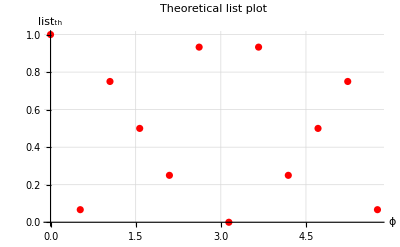

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

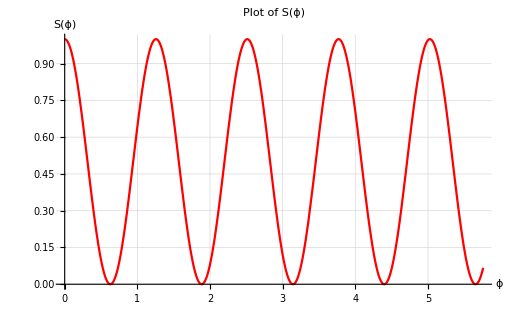

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

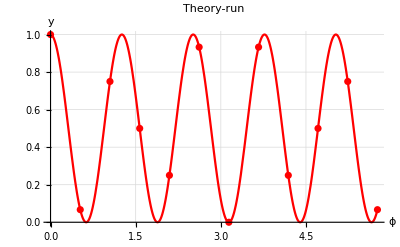

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

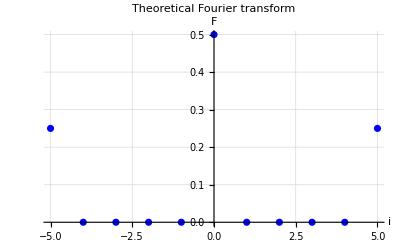

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN NOISE MODEL

1000 shots

```mathematica
data1={1.0,0.061,0.771,0.526,0.225,0.935,0.0,0.9500000000000001,0.225,0.504,0.752,0.062};
data2={0.788,0.069,0.582,0.40800000000000003,0.183,0.723,0.006,0.721,0.192,0.384,0.598,0.079};
data3 = {0.636,0.088,0.484,0.338,0.194,0.559,0.045,0.5710000000000001,0.176,0.327,0.466,0.081};
data4={0.505,0.114,0.40800000000000003,0.307,0.182,0.47900000000000004,0.092,0.464,0.191,0.28800000000000003,0.40700000000000003,0.106};
data5={0.405,0.149,0.318,0.268,0.19,0.384,0.145,0.38,0.213,0.276,0.34500000000000003,0.155};
data6 = {0.34400000000000003,0.189,0.314,0.28600000000000003,0.227,0.359,0.154,0.321,0.211,0.257,0.303,0.195};
data7={0.332,0.225,0.295,0.28,0.263,0.343,0.221,0.332,0.259,0.27,0.318,0.225};
data8={0.301,0.258,0.313,0.281,0.291,0.343,0.278,0.313,0.292,0.28500000000000003,0.34600000000000003,0.267};
data9 = {0.328,0.316,0.34400000000000003,0.336,0.326,0.323,0.309,0.361,0.324,0.356,0.322,0.308};
data10={0.402,0.41200000000000003,0.382,0.366,0.41200000000000003,0.41600000000000004,0.376,0.364,0.404,0.41100000000000003,0.41600000000000004,0.381};
data11 ={0.525,0.487,0.491,0.496,0.483,0.5,0.502,0.47300000000000003,0.511,0.495,0.495,0.508};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.788,0.069,0.582,0.408,0.183,0.723,0.006,0.721,0.192,0.384,0.598,0.079}

12

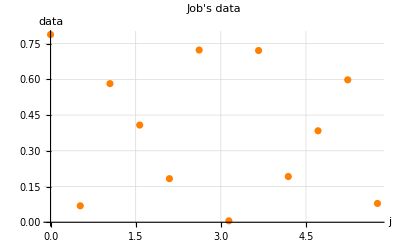

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

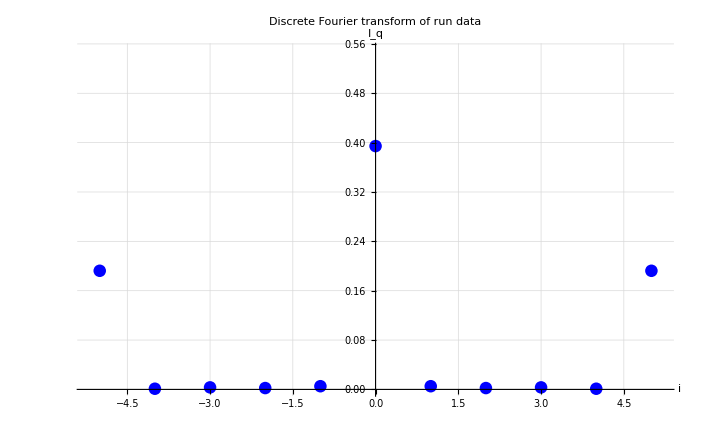

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F11=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data11[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
F5Lower11= 2 √F11[[Length[F11]]];
F5Upper11=√(F11[[n+1]]/2)+√F11[[Length[F11]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10,F5Lower11};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10,F5Upper11};
gamma={0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
retta=Plot[0.5,{x,0,6.5},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

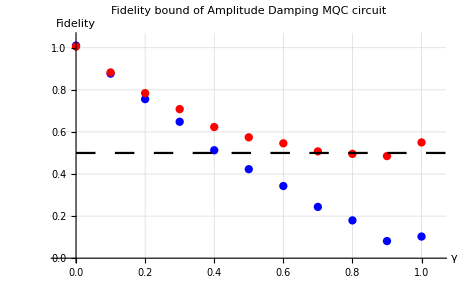

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bound of Amplitude Damping MQC circuit"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.05,1.05},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["γ"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.05,1.05},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

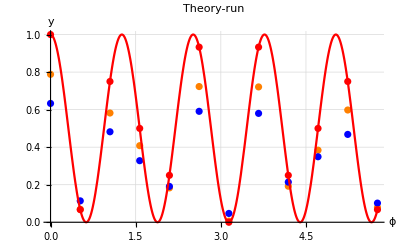

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

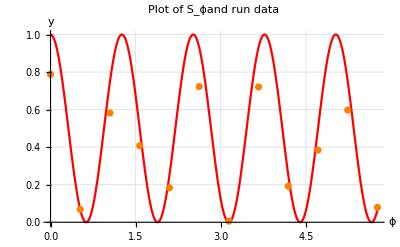

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 Depolarizing (prova)

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

RUN NOISE MODEL

1000 shots

```mathematica
data1={1.0,0.057,0.758,0.523,0.23900000000000002,0.93,0.0,0.93,0.23800000000000002,0.496,0.754,0.068};
data2={0.9530000000000001,0.08,0.7030000000000001,0.48,0.23600000000000002,0.885,0.011,0.891,0.253,0.461,0.724,0.07100000000000001};
data3 = {0.904,0.07200000000000001,0.681,0.448,0.242,0.845,0.035,0.84,0.244,0.47300000000000003,0.686,0.10300000000000001};
data4={0.858,0.106,0.68,0.436,0.267,0.797,0.048,0.804,0.258,0.45,0.653,0.08700000000000001};
data5={0.797,0.113,0.583,0.402,0.251,0.751,0.059000000000000004,0.739,0.214,0.404,0.605,0.096};
data6={0.6890000000000001,0.131,0.536,0.4,0.233,0.63,0.079,0.652,0.23500000000000001,0.405,0.555,0.108};
data7 = {0.591,0.14400000000000002,0.449,0.371,0.229,0.554,0.108,0.55,0.243,0.376,0.494,0.116};
data8={0.352,0.154,0.303,0.248,0.187,0.338,0.157,0.341,0.177,0.245,0.302,0.159};
data9={0.203,0.135,0.179,0.166,0.125,0.191,0.12,0.18,0.152,0.183,0.202,0.126};
data10 = {0.10400000000000001,0.089,0.115,0.10200000000000001,0.113,0.116,0.097,0.114,0.089,0.106,0.10200000000000001,0.099};
data11={0.081,0.078,0.075,0.07100000000000001,0.068,0.07,0.08,0.067,0.061,0.068,0.054,0.067};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.953,0.08,0.703,0.48,0.236,0.885,0.011,0.891,0.253,0.461,0.724,0.071}

12

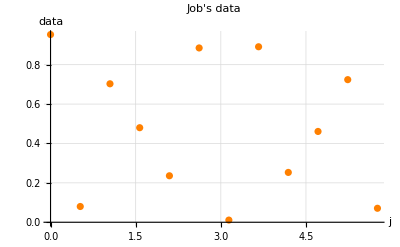

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

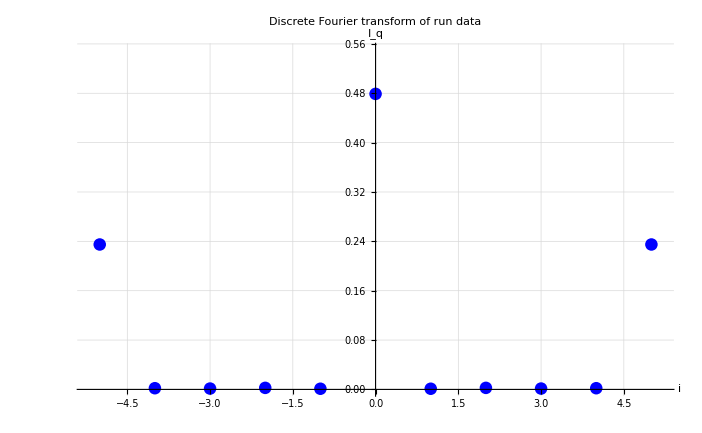

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F11=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data11[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
F5Lower11= 2 √F10[[Length[F10]]];
F5Upper11=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10,F5Lower11};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10,F5Upper11};
p={0,0.01,0.02,0.03,0.05,0.07,0.1,0.2,0.3,0.4,0.5};
Lower=Thread[{p,V5Lower}];
Upper=Thread[{p,V5Upper}];
retta=Plot[0.5,{x,0,6.5},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

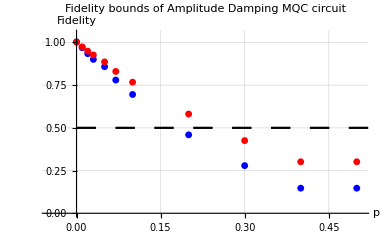

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["p",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Amplitude Damping MQC circuit"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.05,0.51},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{Style["p",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Amplitude Damping MQC circuit"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.05,0.51},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

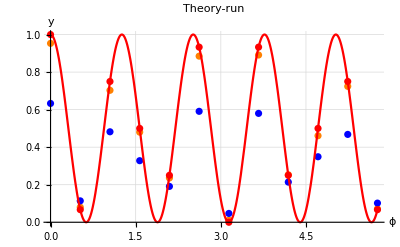

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

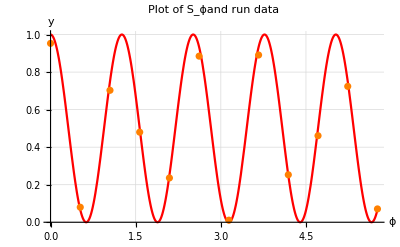

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 Amplitude Damping in way 1

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

RUN NOISE MODEL

1000 shots

```mathematica
data1={0.996,0.063,0.739,0.499,0.24,0.932,0.001,0.926,0.251,0.498,0.761,0.07100000000000001}; (*0.001*)
data2={0.9430000000000001,0.066,0.712,0.47900000000000004,0.229,0.88,0.004,0.875,0.24,0.47600000000000003,0.712,0.06}; (*0.01*)
data3 = {0.771,0.068,0.5650000000000001,0.394,0.198,0.74,0.029,0.72,0.225,0.40700000000000003,0.582,0.093};  (*0.05*)
data4={0.597,0.098,0.454,0.34600000000000003,0.199,0.5750000000000001,0.068,0.592,0.19,0.334,0.466,0.107};  (*0.1*)
data5={0.518,0.14100000000000001,0.44,0.299,0.198,0.496,0.121,0.496,0.222,0.337,0.41500000000000004,0.14200000000000002};  (*0.15*)
data6 = {0.41000000000000003,0.20600000000000002,0.379,0.3,0.243,0.404,0.179,0.431,0.249,0.278,0.38,0.217}; (*0.2*)
data7={0.384,0.271,0.364,0.333,0.272,0.371,0.275,0.394,0.29,0.318,0.341,0.28300000000000003}; (*0.3*)
data8={0.369,0.32,0.384,0.35000000000000003,0.362,0.386,0.342,0.394,0.364,0.369,0.367,0.342};  (*0.4*)
data9={0.37,0.386,0.426,0.381,0.402,0.40900000000000003,0.383,0.40800000000000003,0.399,0.403,0.41200000000000003,0.379};  (*0.5*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.943,0.066,0.712,0.479,0.229,0.88,0.004,0.875,0.24,0.476,0.712,0.06}

12

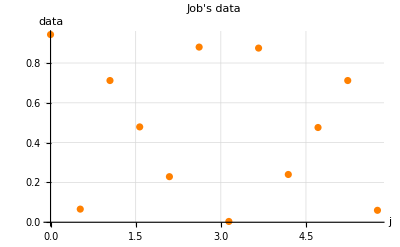

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

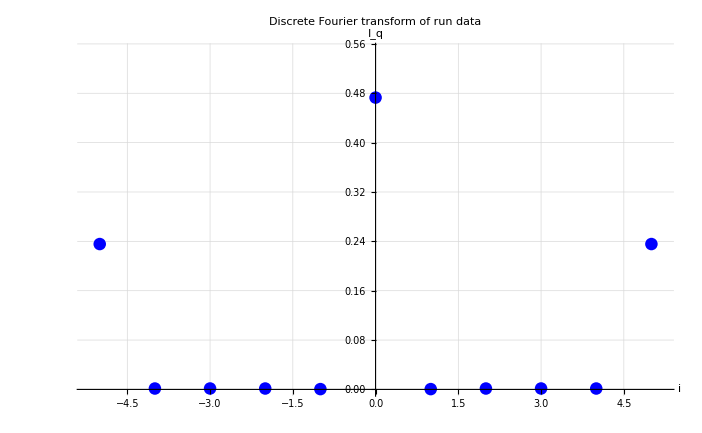

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9};
gamma={0.001,0.01,0.05,0.1,0.15,0.2,0.3,0.4,0.5};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
retta=Plot[0.5,{x,0,0.55},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

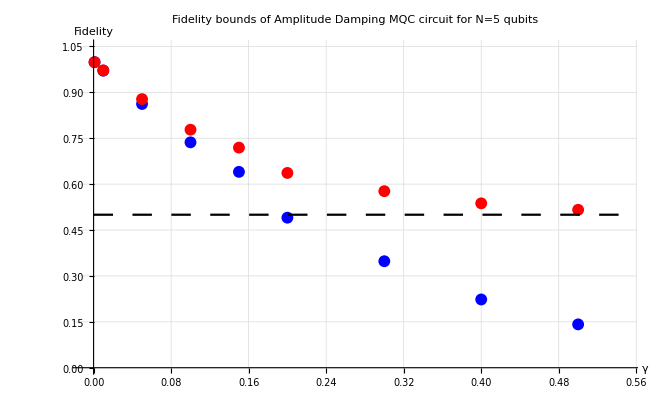

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Amplitude Damping MQC circuit for N=5 qubits"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.01,0.55},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["γ"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.01,0.55},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

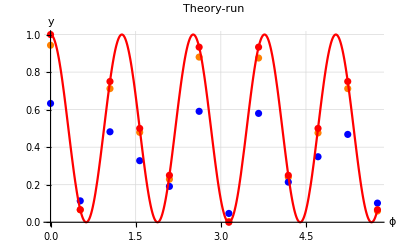

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

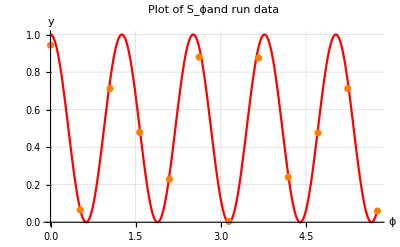

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 Amplitude Damping in way 2

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

RUN NOISE MODEL

1000 shots

```mathematica
data1={0.996,0.08,0.739,0.498,0.271,0.933,0.0,0.922,0.252,0.47900000000000004,0.746,0.073}; (*1*)
data2={0.972,0.067,0.713,0.5,0.23,0.907,0.0,0.9,0.233,0.505,0.726,0.06}; (*5*)
data3 = {0.9410000000000001,0.068,0.6980000000000001,0.491,0.247,0.863,0.006,0.879,0.23700000000000002,0.441,0.708,0.064};  (*10*)
data4={0.898,0.088,0.664,0.458,0.22,0.85,0.013000000000000001,0.8230000000000001,0.20600000000000002,0.423,0.6950000000000001,0.069};  (*20*)
data5={0.8270000000000001,0.068,0.612,0.394,0.20700000000000002,0.762,0.029,0.76,0.221,0.429,0.621,0.074};  (*40*)
data6 = {0.731,0.073,0.583,0.384,0.214,0.709,0.036000000000000004,0.72,0.224,0.383,0.5750000000000001,0.083}; (*60*)
data7={0.679,0.081,0.508,0.379,0.211,0.638,0.054,0.653,0.211,0.34600000000000003,0.514,0.10300000000000001}; (*80*)
data8={0.628,0.116,0.47500000000000003,0.34900000000000003,0.218,0.597,0.07,0.597,0.214,0.306,0.481,0.096};  (*100*)
data9={0.537,0.152,0.438,0.324,0.23600000000000002,0.516,0.11900000000000001,0.46900000000000003,0.228,0.289,0.394,0.136};  (*150*)
data10={0.441,0.185,0.41600000000000004,0.302,0.231,0.421,0.16,0.44,0.23600000000000002,0.31,0.373,0.189};  (*200*)
data11={0.399,0.263,0.34600000000000003,0.327,0.293,0.373,0.256,0.374,0.278,0.34500000000000003,0.358,0.255};  (*300*)
data12={0.37,0.331,0.384,0.379,0.367,0.359,0.322,0.392,0.36,0.359,0.34800000000000003,0.309};  (*500*)
data13={0.394,0.272,0.361,0.34400000000000003,0.318,0.359,0.28,0.361,0.301,0.312,0.372,0.304};  (*400*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.972,0.067,0.713,0.5,0.23,0.907,0.,0.9,0.233,0.505,0.726,0.06}

12

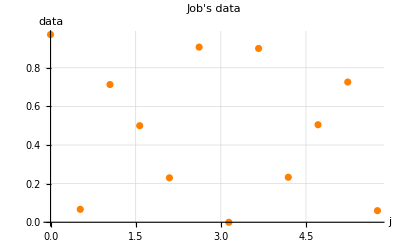

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

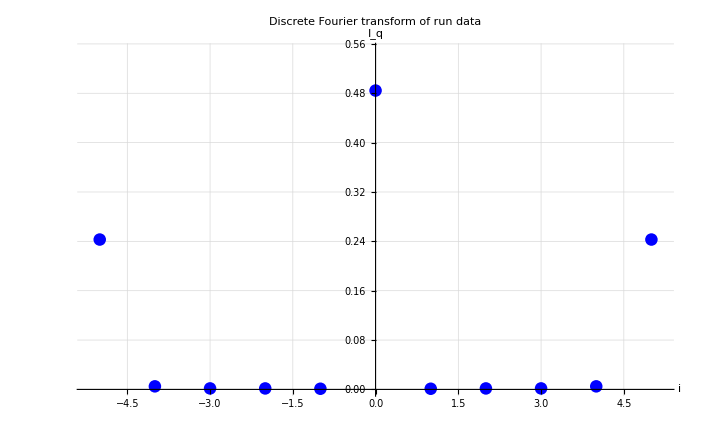

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F11=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data11[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F12=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data12[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F13=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data13[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
F5Lower11= 2 √F11[[Length[F11]]];
F5Upper11=√(F11[[n+1]]/2)+√F11[[Length[F11]]];
F5Lower12= 2 √F12[[Length[F12]]];
F5Upper12=√(F12[[n+1]]/2)+√F12[[Length[F12]]];
F5Lower13= 2 √F13[[Length[F13]]];
F5Upper13=√(F13[[n+1]]/2)+√F13[[Length[F13]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10,F5Lower11,F5Lower12,F5Lower13};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10,F5Upper11,F5Upper12,F5Upper13};
gamma={1,5,10,20,40,60,80,100,150,200,300,500,400};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
retta=Plot[0.5,{x,0,503},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

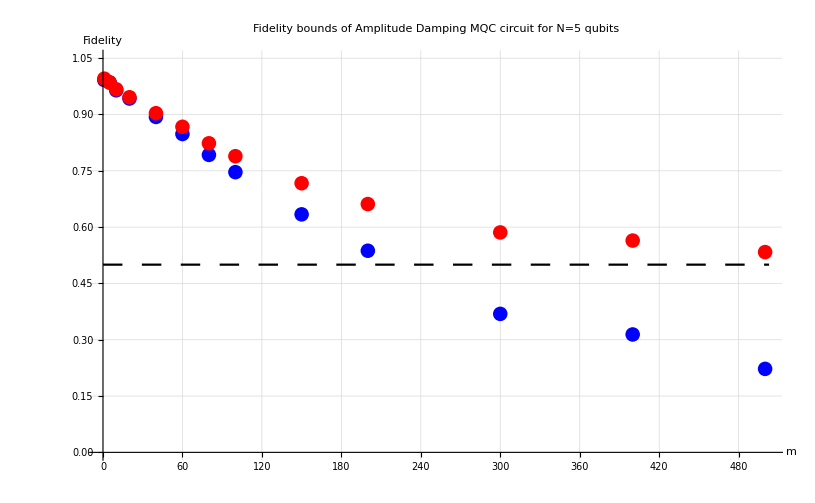

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["m",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Amplitude Damping MQC circuit for N=5 qubits"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.01,503},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["m"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.01,503},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

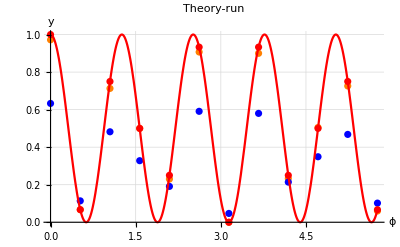

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

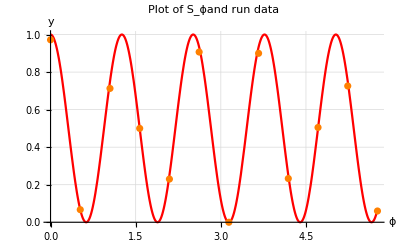

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 Depolarizing in way 1

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

RUN NOISE MODEL

1000 shots

```mathematica
data1={0.984,0.067,0.747,0.508,0.251,0.936,0.004,0.917,0.26,0.511,0.715,0.067}; (*0.001*)
data2={0.869,0.096,0.675,0.449,0.24,0.807,0.038,0.8170000000000001,0.249,0.47200000000000003,0.659,0.094}; (*0.01*)
data3 = {0.494,0.134,0.422,0.28700000000000003,0.193,0.492,0.12,0.46900000000000003,0.178,0.272,0.361,0.14300000000000002};  (*0.05*)
data4={0.276,0.14100000000000001,0.221,0.17400000000000002,0.166,0.23900000000000002,0.14100000000000001,0.229,0.155,0.19,0.2,0.121};  (*0.1*)
data5={0.764,0.115,0.5710000000000001,0.398,0.23500000000000001,0.6990000000000001,0.074,0.739,0.223,0.42,0.5720000000000001,0.11800000000000001};  (*0.02*)
data6 = {0.641,0.129,0.54,0.35000000000000003,0.221,0.617,0.08700000000000001,0.624,0.23900000000000002,0.402,0.523,0.126}; (*0.03*)
data7={0.548,0.149,0.468,0.339,0.217,0.562,0.11,0.539,0.211,0.332,0.464,0.129}; (*0.04*)
data8 = {0.433,0.14,0.333,0.28200000000000003,0.194,0.438,0.11900000000000001,0.41200000000000003,0.232,0.277,0.342,0.148}; (*0.06*)
data9={0.317,0.153,0.277,0.20400000000000001,0.191,0.318,0.116,0.312,0.17400000000000002,0.215,0.296,0.149}; (*0.08*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.869,0.096,0.675,0.449,0.24,0.807,0.038,0.817,0.249,0.472,0.659,0.094}

12

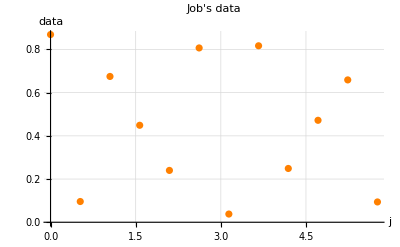

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

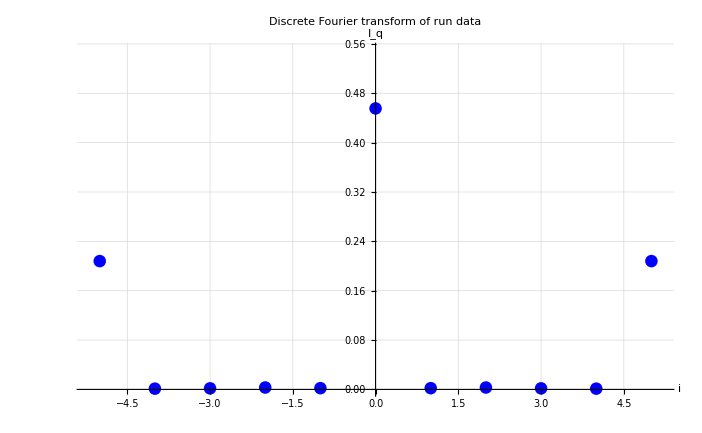

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9};
gamma={0.001,0.01,0.05,0.1,0.02,0.03,0.04,0.06,0.08};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
retta=Plot[0.5,{x,0,0.11},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

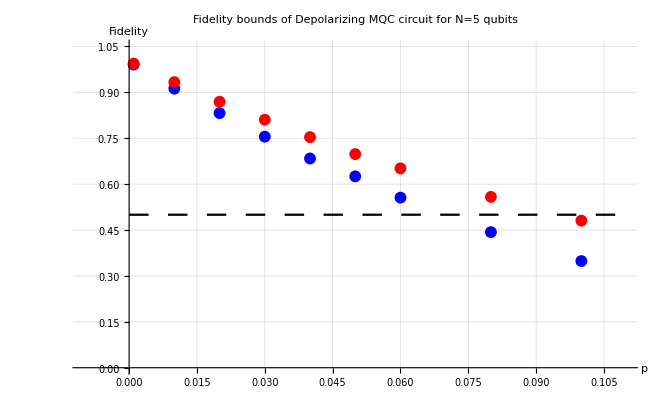

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["p",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Depolarizing MQC circuit for N=5 qubits"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.01,0.11},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["p"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.01,0.11},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

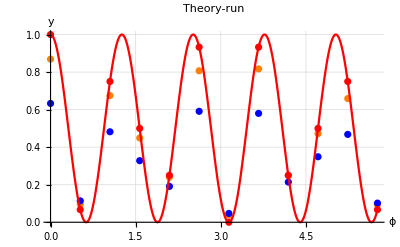

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

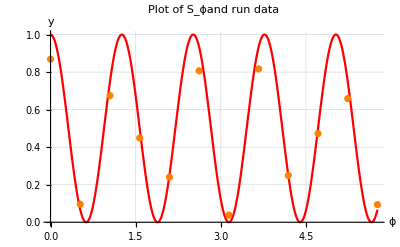

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 Depolarizing in way 2

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

RUN NOISE MODEL

1000 shots

```mathematica
data1={0.984,0.075,0.75,0.492,0.251,0.914,0.003,0.908,0.254,0.496,0.726,0.081}; (*1*)
data2={0.931,0.084,0.68,0.47000000000000003,0.24,0.872,0.021,0.876,0.255,0.462,0.7010000000000001,0.08700000000000001}; (*5*)
data3 = {0.856,0.10300000000000001,0.65,0.49,0.232,0.81,0.042,0.8240000000000001,0.23500000000000001,0.442,0.685,0.089};  (*10*)
data4={0.786,0.10400000000000001,0.5750000000000001,0.405,0.269,0.727,0.068,0.732,0.23600000000000002,0.389,0.598,0.1};  (*20*)
data5={0.5730000000000001,0.126,0.47500000000000003,0.333,0.215,0.552,0.124,0.5740000000000001,0.221,0.34900000000000003,0.47600000000000003,0.138};  (*40*)
data6 = {0.539,0.151,0.394,0.333,0.191,0.481,0.12,0.515,0.20500000000000002,0.317,0.41000000000000003,0.15}; (*50*)
data7={0.468,0.125,0.368,0.277,0.227,0.435,0.11900000000000001,0.41600000000000004,0.211,0.31,0.374,0.165}; (*60*)
data8={0.355,0.136,0.292,0.223,0.196,0.328,0.129,0.322,0.182,0.233,0.315,0.151};  (*80*)
data9={0.28800000000000003,0.121,0.228,0.185,0.169,0.258,0.13,0.26,0.14400000000000002,0.20400000000000001,0.20700000000000002,0.14100000000000001};  (*100*)
data10={0.648,0.129,0.513,0.371,0.241,0.601,0.084,0.633,0.229,0.364,0.495,0.128};  (*30*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.931,0.084,0.68,0.47,0.24,0.872,0.021,0.876,0.255,0.462,0.701,0.087}

12

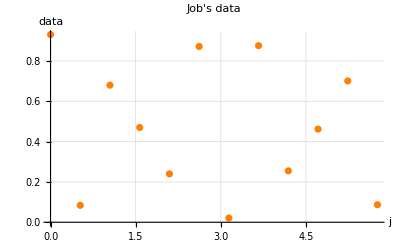

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

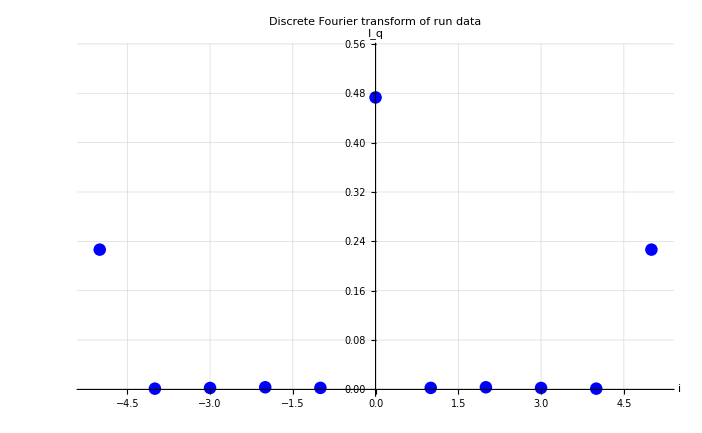

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10};
gamma={1,5,10,20,40,50,60,80,100,30};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
retta=Plot[0.5,{x,0,103},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

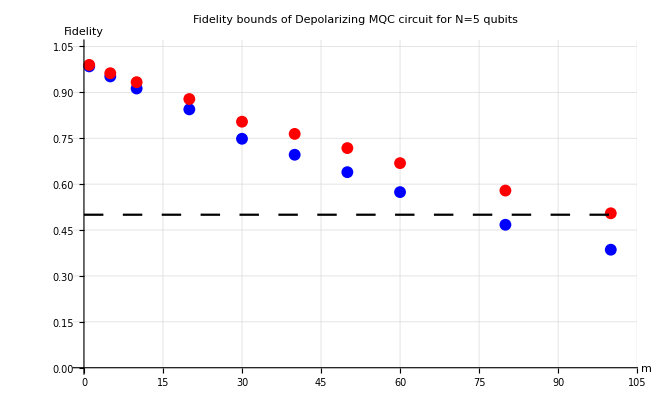

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["m",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds of Depolarizing MQC circuit for N=5 qubits"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.01,103},{0,1.05}}, PlotLegends->{},PlotStyle->{Blue}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["m"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.01,103},{0,1.05}}, PlotLegends->{},PlotStyle->{Red}];
a=Show[P5L,P5U,retta]
```

COMPARE

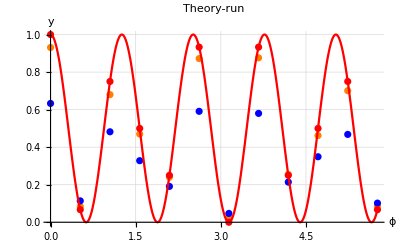

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

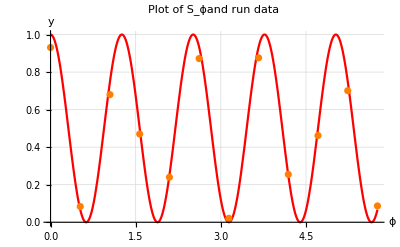

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

## N = 5 random

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

-Graphics-

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

-Graphics-

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

-Graphics-

SIMULATION

```mathematica
data1={0.633,0.114,0.482,0.328,0.191,0.591,0.047,0.58,0.214,0.34900000000000003,0.468,0.10200000000000001};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{0.633,0.114,0.482,0.328,0.191,0.591,0.047,0.58,0.214,0.349,0.468,0.102}

12

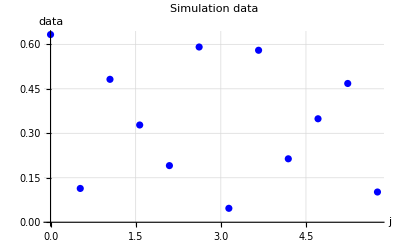

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

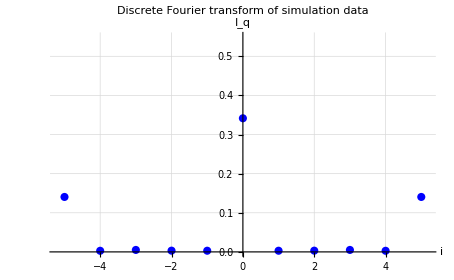

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.749568

0.788053

RUN

8192 shots

```mathematica
data1={0.633,0.114,0.482,0.328,0.191,0.591,0.047,0.58,0.214,0.34900000000000003,0.468,0.10200000000000001};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.633,0.114,0.482,0.328,0.191,0.591,0.047,0.58,0.214,0.349,0.468,0.102}

12

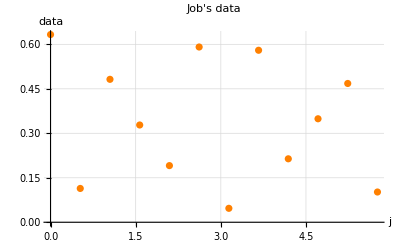

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

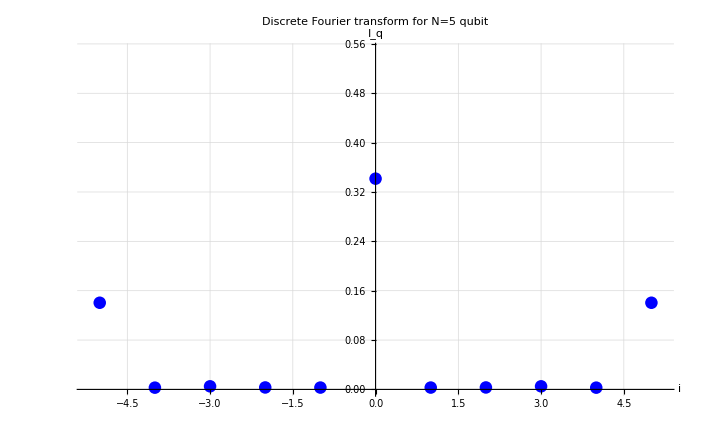

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform for N=5 qubit"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.140463,0.002848,0.00501179,0.00316667,0.00299064,0.341583,0.00299064,0.00316667,0.00501179,0.002848,0.140463}

```mathematica
F4Lower1= 2 √F1[[Length[F1]]]
F4Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.749568

0.788053

COMPARE

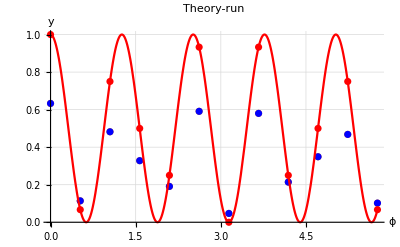

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

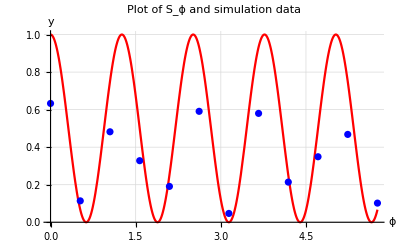

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

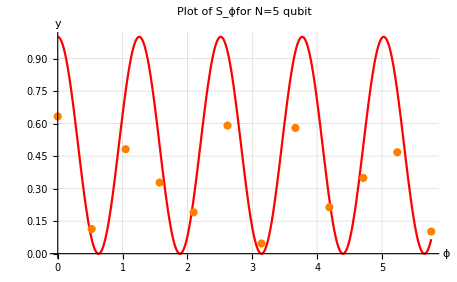

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Plot of S_ϕfor N=5 qubit "],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

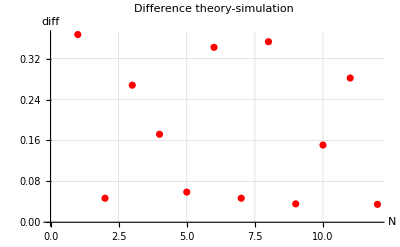

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

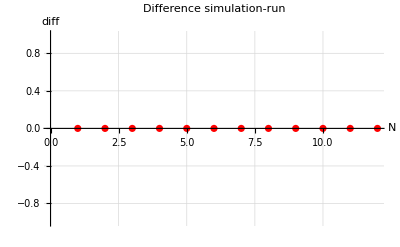

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

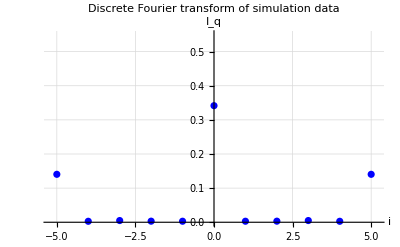

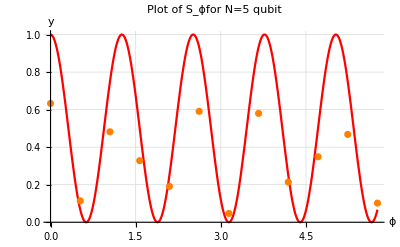

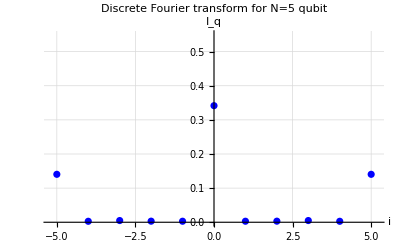

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```